Analiza danych z qc

```mathematica
(*path = "/Users/jakub/Developer/qc/qc/files/";*)
path="/media/Developer/qc/qc/files/";
type = "channels";
noiseParam = 0.96;
outNames = FileNames["*", path<>"outputs/"<>type];
f = ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}];
files = Table[Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}];
combFiles = Table[{f[[i]], files[[i]]}, {i, 1, Length@files}];
```

```mathematica
pythonVectors[v_] := ToExpression@StringSplit[StringReplace[v, { "["-> "", "]"-> ""}], ", "]
```

```mathematica
lengths = files[[All,All,1]][[All,1]];
files = SortBy[Select[combFiles, #[[1]][[2]] ==noiseParam&],#[[1,1]]&][[All,2]];
files[[All,All,3]];
t1 = Table[Mean[files[[All,All,3]][[i]]], {i, 1, Length[files[[All,All,3]]]}];
d1 = Table[Mean[files[[All,All,4]][[i]]], {i, 1, Length[files[[All,All,4]]]}]/2;
t2 = Table[Mean[files[[All,All,6]][[i]]], {i, 1, Length[files[[All,All,6]]]}];
d2 = Table[Mean[files[[All,All,7]][[i]]], {i, 1, Length[files[[All,All,7]]]}]/2;
d3 = Table[Mean[files[[All,All,10]][[i]]], {i, 1, Length[files[[All,All,10]]]}]/2;
dupper1=(1 - t1)/2;
dupper2=(1 - t2);
(*vol = files[[All,All,12]];*)
```

```mathematica
vol1 = vol[[All,1]];
```

```mathematica
vol2 = vol[[All,1]];
```

```mathematica
vol3=vol[[All,1]];
```

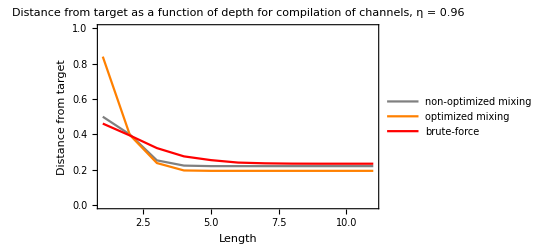

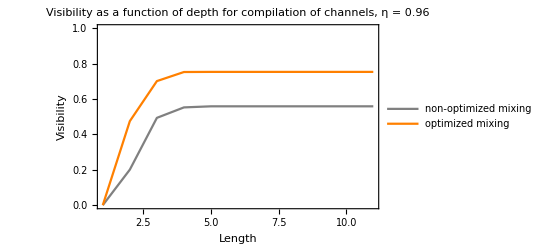

-Graphics-

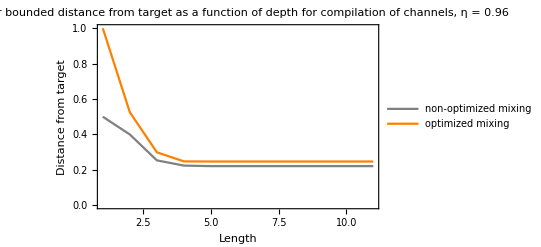

```mathematica
type = If[type=="single_s", "states", If[type=="single_c", "channels", type]];
leg1 = Placed[LineLegend[{"non-optimized mixing","optimized mixing","brute-force"}],{0.75,0.65}];
leg2 =Framed[Column[{LineLegend[{Gray},{4/3 π}],LineLegend[{Green},{"η = 1"}],LineLegend[{Blue},{"η = 0.99"}],LineLegend[{Orange},{"η = 0.95"}]}]];
dofL = ListLinePlot[{d1,d2,d3},FrameLabel->{"Length","Distance from target"},LabelStyle->{GrayLevel[0]}, PlotRange->{{1,11},{0,1}}, Frame-> True, PlotStyle->{Gray, Orange, Red},PlotLabel->"Distance from target as a function of depth
 for compilation of "<>type<>", η = "<>ToString@noiseParam,PlotLegends->leg1]
tofL = ListLinePlot[{t1, t2},FrameLabel->{"Length","Visibility"},LabelStyle->{GrayLevel[0]}, PlotRange->{{1,11},{0,1}}, Frame-> True, PlotStyle->{Gray, Orange, Red},PlotLabel->"Visibility as a function of depth
 for compilation of "<>type<>", η = "<>ToString@noiseParam,PlotLegends->leg1]
volofL = Legended[Show[{ListLinePlot[{vol3,vol2, vol1},PlotStyle->{Orange,Blue, Green},PlotLabel->"Label"],Plot[4/3 Pi, {x,0,11},PlotStyle->Gray]},PlotLabel->HoldForm["Volume of the convex hull of states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{1,11},All}, Frame-> True],Placed[leg2,{1,0.5}]]
dupperofL =ListLinePlot[{dupper1,dupper2},FrameLabel->{"Length","Distance from target"},LabelStyle->{GrayLevel[0]},PlotRange->{{1,11},{0,1}},Frame->True,PlotStyle->{Gray,Orange,Red, Green},PlotLabel->"Upper bounded distance from target as a function of depth
 for compilation of "<>type<>", η = "<>ToString@noiseParam,PlotLegends->leg1]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofL0.99.png", dofL, "PNG", RasterSize-> 2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/tofL0.99.png", tofL, "PNG", RasterSize-> 2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/volofl0.99.png", volofL, "PNG", RasterSize-> 2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofL1.0.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/tofL1.0.png",tofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/volofl1.0.png",volofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/voloflcomb.png",volofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chdistofL0.99.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chtofL0.99.png",tofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chdistofL1.0.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chtofL1.0.png",tofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/dupper1.0.png",dupperofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/dupper0.99.png",dupperofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chdupper1.0.png",dupperofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chdupper0.99.png",dupperofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solochdistofL1.0.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solochtofL1.0.png",tofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solochdistofL0.99.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solochtofL0.99.png",tofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solodistofL1.0.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solotofL1.0.png",tofL,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solodistofL0.99.png",dofL,"PNG",RasterSize->2000];
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/solotofL0.99.png",tofL,"PNG",RasterSize->2000];
```

```mathematica
Lfiltered[L_] := Select[combFiles,#[[1,1]]==L&];
```

{{0.41951,0.394534,0.36861,0.341793,0.315359,0.286713,0.256751,0.226219,0.194052,0.16151},{0.427877,0.40707,0.386336,0.363098,0.337051,0.309291,0.280404,0.251344,0.218771,0.1713},{0.446499,0.426382,0.405191,0.381037,0.354379,0.321714,0.283538,0.24134,0.202648,0.189242}}

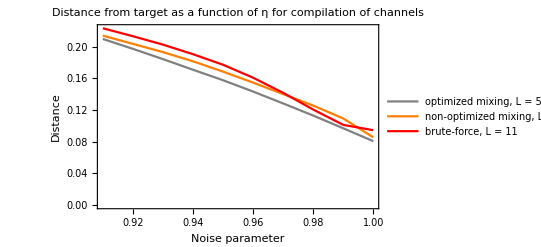

```mathematica
leg3 = Placed[LineLegend[{"optimized mixing, L = 5","non-optimized mixing, L = 5","brute-force, L = 11"}],{0.35,.25}];
noise = Lfiltered[11][[All,1]][[All,2]];
dists= Join[Table[Table[Mean[Lfiltered[5][[All,2,All,j]][[i]]],{i,1,10}],{j,{4,7}}],{Table[Mean[Lfiltered[11][[All,2,All,10]][[i]]],{i,1,10}]}]
dofeta = ListLinePlot[Table[Transpose@{noise,dists[[i]]/2}, {i, 1, 3}],FrameLabel->{"Noise parameter","Distance"},LabelStyle->{GrayLevel[0]},PlotRange->{{0.91,1},Automatic},Frame->True,PlotStyle->{Gray,Orange,Red},PlotLabel->"Distance from target as a function of η 
for compilation of channels",PlotLegends->leg3]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofeta.png",dofeta,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chdistofeta.png",dofeta,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofetaComp.png",dofeta,"PNG",RasterSize->2000];
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/chdistofetaComp.png",dofeta,"PNG",RasterSize->2000];
```

```mathematica
vols = Table[Transpose@{noise,Table[Lfiltered[j][[i,2,All,12]][[1]], {i, 1, 10}]},{j,{3,4,8,11}}]
```

{{{0.91,1.53725},{0.92,1.63866},{0.93,1.74585},{0.94,1.85897},{0.95,1.97831},{0.96,2.10415},{0.97,2.23679},{0.98,2.37651},{0.99,2.52365},{1.,2.67851}},{{0.91,1.62299},{0.92,1.7483},{0.93,1.88485},{0.94,2.03469},{0.95,2.19862},{0.96,2.37524},{0.97,2.56471},{0.98,2.76788},{0.99,2.98564},{1.,3.21895}},{{0.91,1.62605},{0.92,1.75914},{0.93,1.90273},{0.94,2.05836},{0.95,2.23054},{0.96,2.42228},{0.97,2.65013},{0.98,2.94441},{0.99,3.35458},{1.,3.93239}},{{0.91,1.62605},{0.92,1.75914},{0.93,1.90273},{0.94,2.05836},{0.95,2.23054},{0.96,2.42228},{0.97,2.65013},{0.98,2.94441},{0.99,3.35614},{1.,4.08139}}}

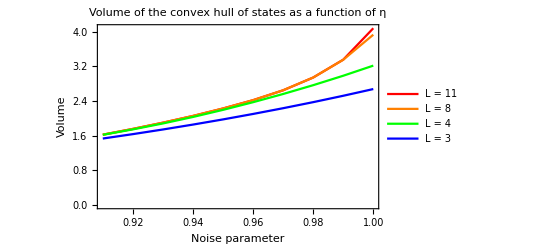

```mathematica
leg4 = Placed[LineLegend[{"L = 11","L = 8","L = 4","L = 3"}],{0.15,.7}];
volofeta=ListLinePlot[Reverse@vols,FrameLabel->{"Noise parameter","Volume"},LabelStyle->{GrayLevel[0]},PlotRange->{{0.91,1},Automatic},Frame->True,PlotStyle->{Red,Orange,Green,Blue},PlotLabel->"Volume of the convex hull of states 
as a function of η",PlotLegends->leg4]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/volofeta.png",volofeta,"PNG",RasterSize->2000];
```

```mathematica
chpointstring = "[[-0.6000000000000001, 0.0, 0.0], [0.0, 0.0, 0.6000000000000001], [0.4242640687119286, 0.7071067811865475, 0.0], [0.4242640687119286, -0.7071067811865475, 0.0], [0.6000000000000001, 0.0, 0.0], [-0.2545584412271572, -0.7071067811865475, 0.0], [-0.2545584412271572, 0.7071067811865475, 0.0], [0.0, 0.0, -0.3600000000000001], [0.0, -0.7071067811865475, 0.2545584412271572], [0.0, 0.7071067811865475, 0.2545584412271572], [7.188244623153863e-17, 1.0, 0.0], [7.188244623153863e-17, -1.0, 0.0], [0.0, -0.7071067811865475, -0.15273506473629436], [0.0, 0.7071067811865475, -0.15273506473629436]]";
```

```mathematica
ConvexHullMesh@ToExpression[StringReplace[chpointstring, {"["->"{","]"->"}","e+":>"*^", "e-" :> "*^-"}]]
```

-Graphics3D-